```mathematica
ColorSSSMatrix[graph_,graphFormat_:FormatGraph,vertices_:Null, sols_]:=Block[{result,bg, sorted,sums},
sorted=Graph[Sort[VertexList[graph]],Sort[EdgeList[graph],EdgeComp]];
sums=Association[];
Table[sums[v]={0,0},{v,VertexList[sorted]}];
result=TableForm[
Table[
bg=None;
Framed[
With[
{
mat=ColorSubMatrix[sols,i,j]
},
sums[i]=sums[i]+mat;
sums[j]=sums[j]+mat;
If[mat[[1]]==0,bg=LightRed];
If[MemberQ[vertices,i]&&MemberQ[vertices,j],bg=LightRed];
If[i==j,bg=LightYellow];
If[EdgeQ[sorted,i<->j],bg=LightBlue];
TableForm[mat]
],
Background->bg
],
{i,VertexList[sorted]},
{j,VertexList[sorted]}],
TableHeadings->{Map[If[MemberQ[vertices,#],Style[#,Bold,Red],#]&,VertexList[sorted]], Map[If[MemberQ[vertices,#],Style[#,Bold,Red],#]&,VertexList[sorted]]},
TableSpacing->{0, 0}
];
{graphFormat[sorted],result,
TableForm[
Map[Framed[{N[#[[1]]/#[[2]]],#[[1]]/#[[2]],TableForm[#]}]&,Values[sums]],
TableHeadings->{Map[If[MemberQ[vertices,#],Style[#,Bold,Red],#]&,Keys[sums]], Map[If[MemberQ[vertices,#],Style[#,Bold,Red],#]&,Keys[sums]]},
TableSpacing->{0, 0}
],
Total[Map[sums[#][[1]]&,Keys[sums]]]/Total[Map[sums[#][[2]]&,Keys[sums]]],
N[Total[Map[sums[#][[1]]&,Keys[sums]]]/Total[Map[sums[#][[2]]&,Keys[sums]]]]
}
]
```

```mathematica
CalcEqual[sols_,v1_,v2_]:=Block[
{couplesols=Map[{Symbol["x"<>ToString[v1]],Symbol["x"<>ToString[v2]]}/.#&,sols]},
Length[Select[couplesols,#[[1]]==#[[2]]&]]
]
```

```mathematica
AlfaBetaPentagon[g_,center_,neighbours_]:=Block[
{ emptyg, sols, sols2,couplesols,f,
alfa,beta,gamma,delta,epsilon, 
alfa1,beta1,gamma1,delta1,epsilon1,
lambda, full},

PrintTemporary["Solving g.." ];
emptyg=VertexDelete[g,center];
sols=Solve[ToEquations[emptyg],SymbolRange[emptyg]];
full=ChromaticPolynomial[g,4];
PrintTemporary["Solved g" ];
lambda=Length[sols];
alfa=CalcEqual[sols,neighbours[[1]],neighbours[[3]]];
beta=CalcEqual[sols,neighbours[[1]],neighbours[[4]]];
gamma=CalcEqual[sols,neighbours[[2]],neighbours[[4]]];
delta=CalcEqual[sols,neighbours[[2]],neighbours[[5]]];
epsilon=CalcEqual[sols,neighbours[[3]],neighbours[[5]]];

PrintTemporary["Solving g 1/3.." ];
f=VertexContract[emptyg,{neighbours[[1]],neighbours[[3]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
delta1=CalcEqual[sols2,neighbours[[2]],neighbours[[5]]];


PrintTemporary["Solving g 1/4.." ];
f=VertexContract[emptyg,{neighbours[[1]],neighbours[[4]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
epsilon1=CalcEqual[sols2,neighbours[[3]],neighbours[[5]]];

PrintTemporary["Solving g 2/4.." ];
f=VertexContract[emptyg,{neighbours[[2]],neighbours[[4]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
alfa1=CalcEqual[sols2,neighbours[[1]],neighbours[[3]]];

PrintTemporary["Solving g 2/5.." ];
f=VertexContract[emptyg,{neighbours[[2]],neighbours[[5]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
beta1=CalcEqual[sols2,neighbours[[1]],neighbours[[4]]];

PrintTemporary["Solving g 3/5.." ];
f=VertexContract[emptyg,{neighbours[[3]],neighbours[[5]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
gamma1=CalcEqual[sols2,neighbours[[2]],neighbours[[4]]];

Column[{
TableForm[
Map[{#}&,{lambda/24,full/24,Style[alfa/24,Red],alfa1/24,Style[beta/24,Red],beta1/24,Style[gamma/24,Red],gamma1/24,Style[delta/24,Red],delta1/24,Style[epsilon/24,Red],epsilon1/24,(alfa+beta+gamma+delta+epsilon)/24}],
TableHeadings->{{λ,Σ,α,α1,β,β1,γ,γ1,δ,δ1,ϵ,ϵ1,α+β+γ+δ+ϵ},None},
TableDirections->Row,
TableAlignments->Center,
TableSpacing->{1, 1}
],
ColorSSSMatrix[VertexDelete[g,center],Graph[#,GraphLayout->"TutteEmbedding", VertexLabels->"Name"]&,neighbours,sols],
{λ->lambda/24,α->alfa/24,α1->alfa1/24,β->beta/24,β1->beta1/24,γ->gamma/24,γ1->gamma1/24,δ->delta/24,δ1->delta1/24,ϵ->epsilon/24,ϵ1->epsilon1/24}
}
]
]
```

```mathematica
AlfaBetaPentagon[Graph[plantri[[1]]],1,{2,3,4,5,6}]
```

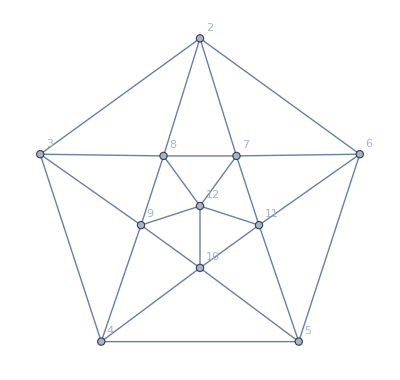
```mathematica
{{{{λ, Σ, α, α1, β, β1, γ, γ1, δ, δ1, ϵ, ϵ1, α+β+γ+δ+ϵ}, {20, 10, 6, 2, 6, 2, 6, 2, 6, 2, 6, 2, 30}}}, {{-Graphics-,{{, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {2, {{20}, {0}}, {{0}, {20}}, {{6}, {14}}, {{6}, {14}}, {{0}, {20}}, {{0}, {20}}, {{0}, {20}}, {{9}, {11}}, {{1}, {19}}, {{9}, {11}}, {{7}, {13}}}, {3, {{0}, {20}}, {{20}, {0}}, {{0}, {20}}, {{6}, {14}}, {{6}, {14}}, {{9}, {11}}, {{0}, {20}}, {{0}, {20}}, {{9}, {11}}, {{1}, {19}}, {{7}, {13}}}, {4, {{6}, {14}}, {{0}, {20}}, {{20}, {0}}, {{0}, {20}}, {{6}, {14}}, {{1}, {19}}, {{9}, {11}}, {{0}, {20}}, {{0}, {20}}, {{9}, {11}}, {{7}, {13}}}, {5, {{6}, {14}}, {{6}, {14}}, {{0}, {20}}, {{20}, {0}}, {{0}, {20}}, {{9}, {11}}, {{1}, {19}}, {{9}, {11}}, {{0}, {20}}, {{0}, {20}}, {{7}, {13}}}, {6, {{0}, {20}}, {{6}, {14}}, {{6}, {14}}, {{0}, {20}}, {{20}, {0}}, {{0}, {20}}, {{9}, {11}}, {{1}, {19}}, {{9}, {11}}, {{0}, {20}}, {{7}, {13}}}, {7, {{0}, {20}}, {{9}, {11}}, {{1}, {19}}, {{9}, {11}}, {{0}, {20}}, {{20}, {0}}, {{0}, {20}}, {{8}, {12}}, {{8}, {12}}, {{0}, {20}}, {{0}, {20}}}, {8, {{0}, {20}}, {{0}, {20}}, {{9}, {11}}, {{1}, {19}}, {{9}, {11}}, {{0}, {20}}, {{20}, {0}}, {{0}, {20}}, {{8}, {12}}, {{8}, {12}}, {{0}, {20}}}, {9, {{9}, {11}}, {{0}, {20}}, {{0}, {20}}, {{9}, {11}}, {{1}, {19}}, {{8}, {12}}, {{0}, {20}}, {{20}, {0}}, {{0}, {20}}, {{8}, {12}}, {{0}, {20}}}, {10, {{1}, {19}}, {{9}, {11}}, {{0}, {20}}, {{0}, {20}}, {{9}, {11}}, {{8}, {12}}, {{8}, {12}}, {{0}, {20}}, {{20}, {0}}, {{0}, {20}}, {{0}, {20}}}, {11, {{9}, {11}}, {{1}, {19}}, {{9}, {11}}, {{0}, {20}}, {{0}, {20}}, {{0}, {20}}, {{8}, {12}}, {{8}, {12}}, {{0}, {20}}, {{20}, {0}}, {{0}, {20}}}, {12, {{7}, {13}}, {{7}, {13}}, {{7}, {13}}, {{7}, {13}}, {{7}, {13}}, {{0}, {20}}, {{0}, {20}}, {{0}, {20}}, {{0}, {20}}, {{0}, {20}}, {{20}, {0}}}},,31/90,0.34444444444444444}}, {{λ->20,α->6,α1->2,β->6,β1->2,γ->6,γ1->2,δ->6,δ1->2,ϵ->6,ϵ1->2}}}
```

```mathematica
AlfaBetaPentagon[Graph[plantri[[2]]],2,{1,3,9,8,7}]
```

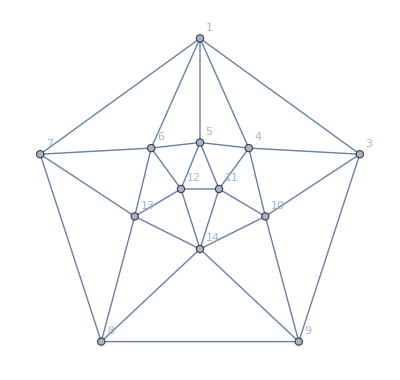
```mathematica
{{{{λ, Σ, α, α1, β, β1, γ, γ1, δ, δ1, ϵ, ϵ1, α+β+γ+δ+ϵ}, {40, 20, 13, 3, 13, 6, 8, 2, 18, 6, 8, 3, 60}}}, {{-Graphics-,{{, 1, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14}, {1, {{40}, {0}}, {{0}, {40}}, {{0}, {40}}, {{0}, {40}}, {{0}, {40}}, {{0}, {40}}, {{13}, {27}}, {{13}, {27}}, {{21}, {19}}, {{17}, {23}}, {{17}, {23}}, {{21}, {19}}, {{1}, {39}}}, {3, {{0}, {40}}, {{40}, {0}}, {{0}, {40}}, {{23}, {17}}, {{12}, {28}}, {{18}, {22}}, {{8}, {32}}, {{0}, {40}}, {{0}, {40}}, {{11}, {29}}, {{2}, {38}}, {{4}, {36}}, {{22}, {18}}}, {4, {{0}, {40}}, {{0}, {40}}, {{40}, {0}}, {{0}, {40}}, {{16}, {24}}, {{12}, {28}}, {{6}, {34}}, {{16}, {24}}, {{0}, {40}}, {{0}, {40}}, {{15}, {25}}, {{5}, {35}}, {{12}, {28}}}, {5, {{0}, {40}}, {{23}, {17}}, {{0}, {40}}, {{40}, {0}}, {{0}, {40}}, {{23}, {17}}, {{4}, {36}}, {{4}, {36}}, {{8}, {32}}, {{0}, {40}}, {{0}, {40}}, {{8}, {32}}, {{23}, {17}}}, {6, {{0}, {40}}, {{12}, {28}}, {{16}, {24}}, {{0}, {40}}, {{40}, {0}}, {{0}, {40}}, {{16}, {24}}, {{6}, {34}}, {{5}, {35}}, {{15}, {25}}, {{0}, {40}}, {{0}, {40}}, {{12}, {28}}}, {7, {{0}, {40}}, {{18}, {22}}, {{12}, {28}}, {{23}, {17}}, {{0}, {40}}, {{40}, {0}}, {{0}, {40}}, {{8}, {32}}, {{4}, {36}}, {{2}, {38}}, {{11}, {29}}, {{0}, {40}}, {{22}, {18}}}, {8, {{13}, {27}}, {{8}, {32}}, {{6}, {34}}, {{4}, {36}}, {{16}, {24}}, {{0}, {40}}, {{40}, {0}}, {{0}, {40}}, {{22}, {18}}, {{10}, {30}}, {{19}, {21}}, {{0}, {40}}, {{0}, {40}}}, {9, {{13}, {27}}, {{0}, {40}}, {{16}, {24}}, {{4}, {36}}, {{6}, {34}}, {{8}, {32}}, {{0}, {40}}, {{40}, {0}}, {{0}, {40}}, {{19}, {21}}, {{10}, {30}}, {{22}, {18}}, {{0}, {40}}}, {10, {{21}, {19}}, {{0}, {40}}, {{0}, {40}}, {{8}, {32}}, {{5}, {35}}, {{4}, {36}}, {{22}, {18}}, {{0}, {40}}, {{40}, {0}}, {{0}, {40}}, {{22}, {18}}, {{8}, {32}}, {{0}, {40}}}, {11, {{17}, {23}}, {{11}, {29}}, {{0}, {40}}, {{0}, {40}}, {{15}, {25}}, {{2}, {38}}, {{10}, {30}}, {{19}, {21}}, {{0}, {40}}, {{40}, {0}}, {{0}, {40}}, {{22}, {18}}, {{0}, {40}}}, {12, {{17}, {23}}, {{2}, {38}}, {{15}, {25}}, {{0}, {40}}, {{0}, {40}}, {{11}, {29}}, {{19}, {21}}, {{10}, {30}}, {{22}, {18}}, {{0}, {40}}, {{40}, {0}}, {{0}, {40}}, {{0}, {40}}}, {13, {{21}, {19}}, {{4}, {36}}, {{5}, {35}}, {{8}, {32}}, {{0}, {40}}, {{0}, {40}}, {{0}, {40}}, {{22}, {18}}, {{8}, {32}}, {{22}, {18}}, {{0}, {40}}, {{40}, {0}}, {{0}, {40}}}, {14, {{1}, {39}}, {{22}, {18}}, {{12}, {28}}, {{23}, {17}}, {{12}, {28}}, {{22}, {18}}, {{0}, {40}}, {{0}, {40}}, {{0}, {40}}, {{0}, {40}}, {{0}, {40}}, {{0}, {40}}, {{40}, {0}}}},,87/251,0.3466135458167331}}, {{λ->40,α->13,α1->3,β->13,β1->6,γ->8,γ1->2,δ->18,δ1->6,ϵ->8,ϵ1->3}}}
```

```mathematica
AlfaBetaPentagon[Graph[plantri[[3]]],2,{1,3,9,8,7}]
```

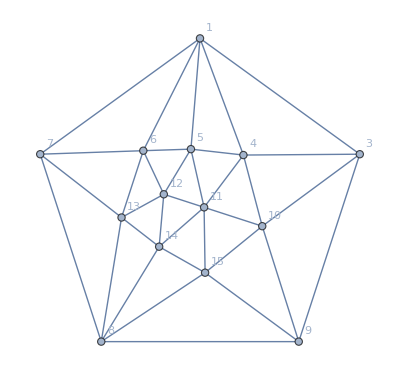
```mathematica
{{{{λ, Σ, α, α1, β, β1, γ, γ1, δ, δ1, ϵ, ϵ1, α+β+γ+δ+ϵ}, {48, 32, 18, 8, 16, 6, 18, 6, 14, 6, 14, 6, 80}}}, {{-Graphics-,{{, 1, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15}, {1, {{48}, {0}}, {{0}, {48}}, {{0}, {48}}, {{0}, {48}}, {{0}, {48}}, {{0}, {48}}, {{16}, {32}}, {{18}, {30}}, {{21}, {27}}, {{19}, {29}}, {{19}, {29}}, {{22}, {26}}, {{4}, {44}}, {{4}, {44}}}, {3, {{0}, {48}}, {{48}, {0}}, {{0}, {48}}, {{19}, {29}}, {{20}, {28}}, {{14}, {34}}, {{18}, {30}}, {{0}, {48}}, {{0}, {48}}, {{19}, {29}}, {{6}, {42}}, {{10}, {38}}, {{6}, {42}}, {{19}, {29}}}, {4, {{0}, {48}}, {{0}, {48}}, {{48}, {0}}, {{0}, {48}}, {{18}, {30}}, {{18}, {30}}, {{4}, {44}}, {{19}, {29}}, {{0}, {48}}, {{0}, {48}}, {{19}, {29}}, {{5}, {43}}, {{18}, {30}}, {{20}, {28}}}, {5, {{0}, {48}}, {{19}, {29}}, {{0}, {48}}, {{48}, {0}}, {{0}, {48}}, {{22}, {26}}, {{4}, {44}}, {{6}, {42}}, {{18}, {30}}, {{0}, {48}}, {{0}, {48}}, {{16}, {32}}, {{22}, {26}}, {{18}, {30}}}, {6, {{0}, {48}}, {{20}, {28}}, {{18}, {30}}, {{0}, {48}}, {{48}, {0}}, {{0}, {48}}, {{22}, {26}}, {{10}, {38}}, {{5}, {43}}, {{21}, {27}}, {{0}, {48}}, {{0}, {48}}, {{16}, {32}}, {{5}, {43}}}, {7, {{0}, {48}}, {{14}, {34}}, {{18}, {30}}, {{22}, {26}}, {{0}, {48}}, {{48}, {0}}, {{0}, {48}}, {{14}, {34}}, {{9}, {39}}, {{3}, {45}}, {{17}, {31}}, {{0}, {48}}, {{22}, {26}}, {{18}, {30}}}, {8, {{16}, {32}}, {{18}, {30}}, {{4}, {44}}, {{4}, {44}}, {{22}, {26}}, {{0}, {48}}, {{48}, {0}}, {{0}, {48}}, {{21}, {27}}, {{19}, {29}}, {{19}, {29}}, {{0}, {48}}, {{0}, {48}}, {{0}, {48}}}, {9, {{18}, {30}}, {{0}, {48}}, {{19}, {29}}, {{6}, {42}}, {{10}, {38}}, {{14}, {34}}, {{0}, {48}}, {{48}, {0}}, {{0}, {48}}, {{19}, {29}}, {{6}, {42}}, {{20}, {28}}, {{19}, {29}}, {{0}, {48}}}, {10, {{21}, {27}}, {{0}, {48}}, {{0}, {48}}, {{18}, {30}}, {{5}, {43}}, {{9}, {39}}, {{21}, {27}}, {{0}, {48}}, {{48}, {0}}, {{0}, {48}}, {{20}, {28}}, {{5}, {43}}, {{18}, {30}}, {{0}, {48}}}, {11, {{19}, {29}}, {{19}, {29}}, {{0}, {48}}, {{0}, {48}}, {{21}, {27}}, {{3}, {45}}, {{19}, {29}}, {{19}, {29}}, {{0}, {48}}, {{48}, {0}}, {{0}, {48}}, {{21}, {27}}, {{0}, {48}}, {{0}, {48}}}, {12, {{19}, {29}}, {{6}, {42}}, {{19}, {29}}, {{0}, {48}}, {{0}, {48}}, {{17}, {31}}, {{19}, {29}}, {{6}, {42}}, {{20}, {28}}, {{0}, {48}}, {{48}, {0}}, {{0}, {48}}, {{0}, {48}}, {{19}, {29}}}, {13, {{22}, {26}}, {{10}, {38}}, {{5}, {43}}, {{16}, {32}}, {{0}, {48}}, {{0}, {48}}, {{0}, {48}}, {{20}, {28}}, {{5}, {43}}, {{21}, {27}}, {{0}, {48}}, {{48}, {0}}, {{0}, {48}}, {{18}, {30}}}, {14, {{4}, {44}}, {{6}, {42}}, {{18}, {30}}, {{22}, {26}}, {{16}, {32}}, {{22}, {26}}, {{0}, {48}}, {{19}, {29}}, {{18}, {30}}, {{0}, {48}}, {{0}, {48}}, {{0}, {48}}, {{48}, {0}}, {{0}, {48}}}, {15, {{4}, {44}}, {{19}, {29}}, {{20}, {28}}, {{18}, {30}}, {{5}, {43}}, {{18}, {30}}, {{0}, {48}}, {{0}, {48}}, {{0}, {48}}, {{0}, {48}}, {{19}, {29}}, {{18}, {30}}, {{0}, {48}}, {{48}, {0}}}},,401/1167,0.34361610968294776}}, {{λ->48,α->18,α1->8,β->16,β1->6,γ->18,γ1->6,δ->14,δ1->6,ϵ->14,ϵ1->6}}}
```

```mathematica
AlfaBetaPentagon[EdgeDelete[Graph[plantri[[3]]],7<->6],2,{1,3,9,8,7}]
```

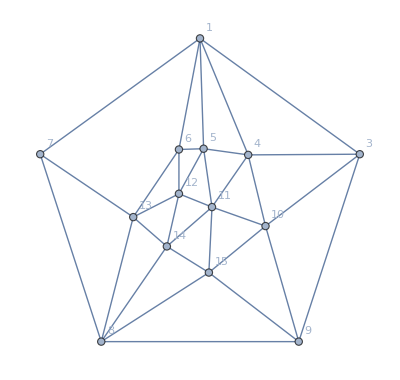
```mathematica
{{{{λ, Σ, α, α1, β, β1, γ, γ1, δ, δ1, ϵ, ϵ1, α+β+γ+δ+ϵ}, {82, 48, 28, 10, 32, 8, 22, 8, 18, 8, 30, 14, 130}}}, {{-Graphics-,{{, 1, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15}, {1, {{82}, {0}}, {{0}, {82}}, {{0}, {82}}, {{0}, {82}}, {{0}, {82}}, {{0}, {82}}, {{32}, {50}}, {{28}, {54}}, {{37}, {45}}, {{35}, {47}}, {{36}, {46}}, {{32}, {50}}, {{5}, {77}}, {{6}, {76}}}, {3, {{0}, {82}}, {{82}, {0}}, {{0}, {82}}, {{39}, {43}}, {{24}, {58}}, {{18}, {64}}, {{22}, {60}}, {{0}, {82}}, {{0}, {82}}, {{27}, {55}}, {{10}, {72}}, {{24}, {58}}, {{10}, {72}}, {{39}, {43}}}, {4, {{0}, {82}}, {{0}, {82}}, {{82}, {0}}, {{0}, {82}}, {{40}, {42}}, {{40}, {42}}, {{8}, {74}}, {{35}, {47}}, {{0}, {82}}, {{0}, {82}}, {{26}, {56}}, {{7}, {75}}, {{39}, {43}}, {{28}, {54}}}, {5, {{0}, {82}}, {{39}, {43}}, {{0}, {82}}, {{82}, {0}}, {{0}, {82}}, {{22}, {60}}, {{9}, {73}}, {{8}, {74}}, {{26}, {56}}, {{0}, {82}}, {{0}, {82}}, {{32}, {50}}, {{29}, {53}}, {{38}, {44}}}, {6, {{0}, {82}}, {{24}, {58}}, {{40}, {42}}, {{0}, {82}}, {{82}, {0}}, {{34}, {48}}, {{22}, {60}}, {{26}, {56}}, {{9}, {73}}, {{27}, {55}}, {{0}, {82}}, {{0}, {82}}, {{39}, {43}}, {{10}, {72}}}, {7, {{0}, {82}}, {{18}, {64}}, {{40}, {42}}, {{22}, {60}}, {{34}, {48}}, {{82}, {0}}, {{0}, {82}}, {{30}, {52}}, {{13}, {69}}, {{9}, {73}}, {{17}, {65}}, {{0}, {82}}, {{45}, {37}}, {{23}, {59}}}, {8, {{32}, {50}}, {{22}, {60}}, {{8}, {74}}, {{9}, {73}}, {{22}, {60}}, {{0}, {82}}, {{82}, {0}}, {{0}, {82}}, {{43}, {39}}, {{25}, {57}}, {{42}, {40}}, {{0}, {82}}, {{0}, {82}}, {{0}, {82}}}, {9, {{28}, {54}}, {{0}, {82}}, {{35}, {47}}, {{8}, {74}}, {{26}, {56}}, {{30}, {52}}, {{0}, {82}}, {{82}, {0}}, {{0}, {82}}, {{35}, {47}}, {{7}, {75}}, {{30}, {52}}, {{36}, {46}}, {{0}, {82}}}, {10, {{37}, {45}}, {{0}, {82}}, {{0}, {82}}, {{26}, {56}}, {{9}, {73}}, {{13}, {69}}, {{43}, {39}}, {{0}, {82}}, {{82}, {0}}, {{0}, {82}}, {{41}, {41}}, {{7}, {75}}, {{25}, {57}}, {{0}, {82}}}, {11, {{35}, {47}}, {{27}, {55}}, {{0}, {82}}, {{0}, {82}}, {{27}, {55}}, {{9}, {73}}, {{25}, {57}}, {{35}, {47}}, {{0}, {82}}, {{82}, {0}}, {{0}, {82}}, {{37}, {45}}, {{0}, {82}}, {{0}, {82}}}, {12, {{36}, {46}}, {{10}, {72}}, {{26}, {56}}, {{0}, {82}}, {{0}, {82}}, {{17}, {65}}, {{42}, {40}}, {{7}, {75}}, {{41}, {41}}, {{0}, {82}}, {{82}, {0}}, {{0}, {82}}, {{0}, {82}}, {{26}, {56}}}, {13, {{32}, {50}}, {{24}, {58}}, {{7}, {75}}, {{32}, {50}}, {{0}, {82}}, {{0}, {82}}, {{0}, {82}}, {{30}, {52}}, {{7}, {75}}, {{37}, {45}}, {{0}, {82}}, {{82}, {0}}, {{0}, {82}}, {{34}, {48}}}, {14, {{5}, {77}}, {{10}, {72}}, {{39}, {43}}, {{29}, {53}}, {{39}, {43}}, {{45}, {37}}, {{0}, {82}}, {{36}, {46}}, {{25}, {57}}, {{0}, {82}}, {{0}, {82}}, {{0}, {82}}, {{82}, {0}}, {{0}, {82}}}, {15, {{6}, {76}}, {{39}, {43}}, {{28}, {54}}, {{38}, {44}}, {{10}, {72}}, {{23}, {59}}, {{0}, {82}}, {{0}, {82}}, {{0}, {82}}, {{0}, {82}}, {{26}, {56}}, {{34}, {48}}, {{0}, {82}}, {{82}, {0}}}},,2077/5959,0.3485484141634502}}, {{λ->82,α->28,α1->10,β->32,β1->8,γ->22,γ1->8,δ->18,δ1->8,ϵ->30,ϵ1->14}}}
```

```mathematica
AlfaBetaPentagon[EdgeContract[Graph[plantri[[3]]],7<->6],2,{1,3,9,8,6}]
```

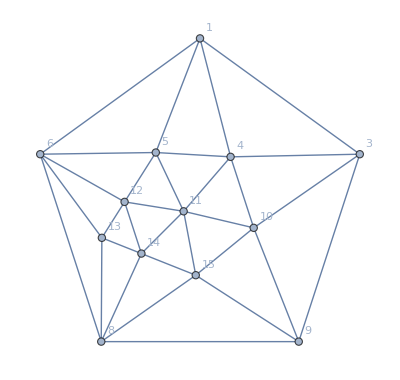
```mathematica
{{{{λ, Σ, α, α1, β, β1, γ, γ1, δ, δ1, ϵ, ϵ1, α+β+γ+δ+ϵ}, {34, 16, 10, 2, 16, 2, 4, 2, 4, 2, 16, 8, 50}}}, {{-Graphics-,{{, 1, 3, 4, 5, 6, 8, 9, 10, 11, 12, 13, 14, 15}, {1, {{34}, {0}}, {{0}, {34}}, {{0}, {34}}, {{0}, {34}}, {{0}, {34}}, {{16}, {18}}, {{10}, {24}}, {{16}, {18}}, {{16}, {18}}, {{17}, {17}}, {{10}, {24}}, {{1}, {33}}, {{2}, {32}}}, {3, {{0}, {34}}, {{34}, {0}}, {{0}, {34}}, {{20}, {14}}, {{4}, {30}}, {{4}, {30}}, {{0}, {34}}, {{0}, {34}}, {{8}, {26}}, {{4}, {30}}, {{14}, {20}}, {{4}, {30}}, {{20}, {14}}}, {4, {{0}, {34}}, {{0}, {34}}, {{34}, {0}}, {{0}, {34}}, {{22}, {12}}, {{4}, {30}}, {{16}, {18}}, {{0}, {34}}, {{0}, {34}}, {{7}, {27}}, {{2}, {32}}, {{21}, {13}}, {{8}, {26}}}, {5, {{0}, {34}}, {{20}, {14}}, {{0}, {34}}, {{34}, {0}}, {{0}, {34}}, {{5}, {29}}, {{2}, {32}}, {{8}, {26}}, {{0}, {34}}, {{0}, {34}}, {{16}, {18}}, {{7}, {27}}, {{20}, {14}}}, {6, {{0}, {34}}, {{4}, {30}}, {{22}, {12}}, {{0}, {34}}, {{34}, {0}}, {{0}, {34}}, {{16}, {18}}, {{4}, {30}}, {{6}, {28}}, {{0}, {34}}, {{0}, {34}}, {{23}, {11}}, {{5}, {29}}}, {8, {{16}, {18}}, {{4}, {30}}, {{4}, {30}}, {{5}, {29}}, {{0}, {34}}, {{34}, {0}}, {{0}, {34}}, {{22}, {12}}, {{6}, {28}}, {{23}, {11}}, {{0}, {34}}, {{0}, {34}}, {{0}, {34}}}, {9, {{10}, {24}}, {{0}, {34}}, {{16}, {18}}, {{2}, {32}}, {{16}, {18}}, {{0}, {34}}, {{34}, {0}}, {{0}, {34}}, {{16}, {18}}, {{1}, {33}}, {{10}, {24}}, {{17}, {17}}, {{0}, {34}}}, {10, {{16}, {18}}, {{0}, {34}}, {{0}, {34}}, {{8}, {26}}, {{4}, {30}}, {{22}, {12}}, {{0}, {34}}, {{34}, {0}}, {{0}, {34}}, {{21}, {13}}, {{2}, {32}}, {{7}, {27}}, {{0}, {34}}}, {11, {{16}, {18}}, {{8}, {26}}, {{0}, {34}}, {{0}, {34}}, {{6}, {28}}, {{6}, {28}}, {{16}, {18}}, {{0}, {34}}, {{34}, {0}}, {{0}, {34}}, {{16}, {18}}, {{0}, {34}}, {{0}, {34}}}, {12, {{17}, {17}}, {{4}, {30}}, {{7}, {27}}, {{0}, {34}}, {{0}, {34}}, {{23}, {11}}, {{1}, {33}}, {{21}, {13}}, {{0}, {34}}, {{34}, {0}}, {{0}, {34}}, {{0}, {34}}, {{7}, {27}}}, {13, {{10}, {24}}, {{14}, {20}}, {{2}, {32}}, {{16}, {18}}, {{0}, {34}}, {{0}, {34}}, {{10}, {24}}, {{2}, {32}}, {{16}, {18}}, {{0}, {34}}, {{34}, {0}}, {{0}, {34}}, {{16}, {18}}}, {14, {{1}, {33}}, {{4}, {30}}, {{21}, {13}}, {{7}, {27}}, {{23}, {11}}, {{0}, {34}}, {{17}, {17}}, {{7}, {27}}, {{0}, {34}}, {{0}, {34}}, {{0}, {34}}, {{34}, {0}}, {{0}, {34}}}, {15, {{2}, {32}}, {{20}, {14}}, {{8}, {26}}, {{20}, {14}}, {{5}, {29}}, {{0}, {34}}, {{0}, {34}}, {{0}, {34}}, {{0}, {34}}, {{7}, {27}}, {{16}, {18}}, {{0}, {34}}, {{34}, {0}}}},,743/2130,0.3488262910798122}}, {{λ->34,α->10,α1->2,β->16,β1->2,γ->4,γ1->2,δ->4,δ1->2,ϵ->16,ϵ1->8}}}
```

```mathematica
AlfaBetaPentagon[Graph[plantri[[4]]],1,{2,6,5,4,3}]
```

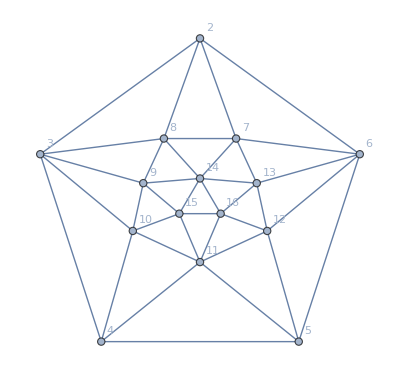
```mathematica
{{{{λ, Σ, α, α1, β, β1, γ, γ1, δ, δ1, ϵ, ϵ1, α+β+γ+δ+ϵ}, {60, 30, 14, 2, 14, 10, 14, 6, 34, 10, 14, 2, 90}}}, {{-Graphics-,{{, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16}, {2, {{60}, {0}}, {{0}, {60}}, {{14}, {46}}, {{14}, {46}}, {{0}, {60}}, {{0}, {60}}, {{0}, {60}}, {{27}, {33}}, {{20}, {40}}, {{12}, {48}}, {{20}, {40}}, {{27}, {33}}, {{16}, {44}}, {{9}, {51}}, {{9}, {51}}}, {3, {{0}, {60}}, {{60}, {0}}, {{0}, {60}}, {{14}, {46}}, {{34}, {26}}, {{17}, {43}}, {{0}, {60}}, {{0}, {60}}, {{0}, {60}}, {{36}, {24}}, {{8}, {52}}, {{5}, {55}}, {{36}, {24}}, {{16}, {44}}, {{4}, {56}}}, {4, {{14}, {46}}, {{0}, {60}}, {{60}, {0}}, {{0}, {60}}, {{14}, {46}}, {{19}, {41}}, {{21}, {39}}, {{24}, {36}}, {{0}, {60}}, {{0}, {60}}, {{26}, {34}}, {{11}, {49}}, {{4}, {56}}, {{27}, {33}}, {{18}, {42}}}, {5, {{14}, {46}}, {{14}, {46}}, {{0}, {60}}, {{60}, {0}}, {{0}, {60}}, {{21}, {39}}, {{19}, {41}}, {{11}, {49}}, {{26}, {34}}, {{0}, {60}}, {{0}, {60}}, {{24}, {36}}, {{4}, {56}}, {{18}, {42}}, {{27}, {33}}}, {6, {{0}, {60}}, {{34}, {26}}, {{14}, {46}}, {{0}, {60}}, {{60}, {0}}, {{0}, {60}}, {{17}, {43}}, {{5}, {55}}, {{8}, {52}}, {{36}, {24}}, {{0}, {60}}, {{0}, {60}}, {{36}, {24}}, {{4}, {56}}, {{16}, {44}}}, {7, {{0}, {60}}, {{17}, {43}}, {{19}, {41}}, {{21}, {39}}, {{0}, {60}}, {{60}, {0}}, {{0}, {60}}, {{24}, {36}}, {{10}, {50}}, {{3}, {57}}, {{26}, {34}}, {{0}, {60}}, {{0}, {60}}, {{21}, {39}}, {{26}, {34}}}, {8, {{0}, {60}}, {{0}, {60}}, {{21}, {39}}, {{19}, {41}}, {{17}, {43}}, {{0}, {60}}, {{60}, {0}}, {{0}, {60}}, {{26}, {34}}, {{3}, {57}}, {{10}, {50}}, {{24}, {36}}, {{0}, {60}}, {{26}, {34}}, {{21}, {39}}}, {9, {{27}, {33}}, {{0}, {60}}, {{24}, {36}}, {{11}, {49}}, {{5}, {55}}, {{24}, {36}}, {{0}, {60}}, {{60}, {0}}, {{0}, {60}}, {{17}, {43}}, {{11}, {49}}, {{22}, {38}}, {{0}, {60}}, {{0}, {60}}, {{24}, {36}}}, {10, {{20}, {40}}, {{0}, {60}}, {{0}, {60}}, {{26}, {34}}, {{8}, {52}}, {{10}, {50}}, {{26}, {34}}, {{0}, {60}}, {{60}, {0}}, {{0}, {60}}, {{18}, {42}}, {{11}, {49}}, {{16}, {44}}, {{0}, {60}}, {{27}, {33}}}, {11, {{12}, {48}}, {{36}, {24}}, {{0}, {60}}, {{0}, {60}}, {{36}, {24}}, {{3}, {57}}, {{3}, {57}}, {{17}, {43}}, {{0}, {60}}, {{60}, {0}}, {{0}, {60}}, {{17}, {43}}, {{36}, {24}}, {{0}, {60}}, {{0}, {60}}}, {12, {{20}, {40}}, {{8}, {52}}, {{26}, {34}}, {{0}, {60}}, {{0}, {60}}, {{26}, {34}}, {{10}, {50}}, {{11}, {49}}, {{18}, {42}}, {{0}, {60}}, {{60}, {0}}, {{0}, {60}}, {{16}, {44}}, {{27}, {33}}, {{0}, {60}}}, {13, {{27}, {33}}, {{5}, {55}}, {{11}, {49}}, {{24}, {36}}, {{0}, {60}}, {{0}, {60}}, {{24}, {36}}, {{22}, {38}}, {{11}, {49}}, {{17}, {43}}, {{0}, {60}}, {{60}, {0}}, {{0}, {60}}, {{24}, {36}}, {{0}, {60}}}, {14, {{16}, {44}}, {{36}, {24}}, {{4}, {56}}, {{4}, {56}}, {{36}, {24}}, {{0}, {60}}, {{0}, {60}}, {{0}, {60}}, {{16}, {44}}, {{36}, {24}}, {{16}, {44}}, {{0}, {60}}, {{60}, {0}}, {{0}, {60}}, {{0}, {60}}}, {15, {{9}, {51}}, {{16}, {44}}, {{27}, {33}}, {{18}, {42}}, {{4}, {56}}, {{21}, {39}}, {{26}, {34}}, {{0}, {60}}, {{0}, {60}}, {{0}, {60}}, {{27}, {33}}, {{24}, {36}}, {{0}, {60}}, {{60}, {0}}, {{0}, {60}}}, {16, {{9}, {51}}, {{4}, {56}}, {{18}, {42}}, {{27}, {33}}, {{16}, {44}}, {{26}, {34}}, {{21}, {39}}, {{24}, {36}}, {{27}, {33}}, {{0}, {60}}, {{0}, {60}}, {{0}, {60}}, {{0}, {60}}, {{0}, {60}}, {{60}, {0}}}},,19/56,0.3392857142857143}}, {{λ->60,α->14,α1->2,β->14,β1->10,γ->14,γ1->6,δ->34,δ1->10,ϵ->14,ϵ1->2}}}
```

```mathematica
AlfaBetaPentagon[Graph[plantri[[5]]],1,{4,3,2,6,5}]
```

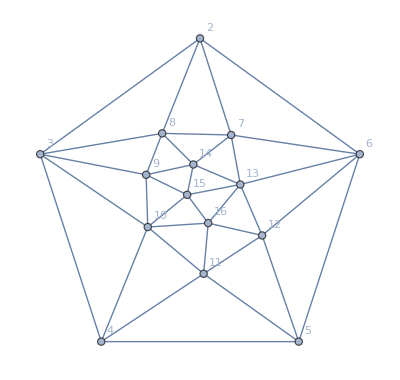
```mathematica
{{{{λ, Σ, α, α1, β, β1, γ, γ1, δ, δ1, ϵ, ϵ1, α+β+γ+δ+ϵ}, {58, 27, 14, 8, 20, 7, 25, 6, 14, 2, 12, 4, 85}}}, {{-Graphics-,{{, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16}, {2, {{58}, {0}}, {{0}, {58}}, {{14}, {44}}, {{12}, {46}}, {{0}, {58}}, {{0}, {58}}, {{0}, {58}}, {{23}, {35}}, {{20}, {38}}, {{14}, {44}}, {{22}, {36}}, {{22}, {36}}, {{22}, {36}}, {{5}, {53}}, {{8}, {50}}}, {3, {{0}, {58}}, {{58}, {0}}, {{0}, {58}}, {{14}, {44}}, {{25}, {33}}, {{25}, {33}}, {{0}, {58}}, {{0}, {58}}, {{0}, {58}}, {{26}, {32}}, {{9}, {49}}, {{2}, {56}}, {{23}, {35}}, {{28}, {30}}, {{18}, {40}}}, {4, {{14}, {44}}, {{0}, {58}}, {{58}, {0}}, {{0}, {58}}, {{20}, {38}}, {{17}, {41}}, {{16}, {42}}, {{24}, {34}}, {{0}, {58}}, {{0}, {58}}, {{24}, {34}}, {{4}, {54}}, {{10}, {48}}, {{17}, {41}}, {{26}, {32}}}, {5, {{12}, {46}}, {{14}, {44}}, {{0}, {58}}, {{58}, {0}}, {{0}, {58}}, {{15}, {43}}, {{24}, {34}}, {{9}, {49}}, {{32}, {26}}, {{0}, {58}}, {{0}, {58}}, {{32}, {26}}, {{8}, {50}}, {{4}, {54}}, {{16}, {42}}}, {6, {{0}, {58}}, {{25}, {33}}, {{20}, {38}}, {{0}, {58}}, {{58}, {0}}, {{0}, {58}}, {{18}, {40}}, {{7}, {51}}, {{2}, {56}}, {{26}, {32}}, {{0}, {58}}, {{0}, {58}}, {{25}, {33}}, {{19}, {39}}, {{26}, {32}}}, {7, {{0}, {58}}, {{25}, {33}}, {{17}, {41}}, {{15}, {43}}, {{0}, {58}}, {{58}, {0}}, {{0}, {58}}, {{23}, {35}}, {{3}, {55}}, {{11}, {47}}, {{23}, {35}}, {{0}, {58}}, {{0}, {58}}, {{27}, {31}}, {{19}, {39}}}, {8, {{0}, {58}}, {{0}, {58}}, {{16}, {42}}, {{24}, {34}}, {{18}, {40}}, {{0}, {58}}, {{58}, {0}}, {{0}, {58}}, {{29}, {29}}, {{10}, {48}}, {{8}, {50}}, {{29}, {29}}, {{0}, {58}}, {{18}, {40}}, {{6}, {52}}}, {9, {{23}, {35}}, {{0}, {58}}, {{24}, {34}}, {{9}, {49}}, {{7}, {51}}, {{23}, {35}}, {{0}, {58}}, {{58}, {0}}, {{0}, {58}}, {{18}, {40}}, {{10}, {48}}, {{19}, {39}}, {{0}, {58}}, {{0}, {58}}, {{24}, {34}}}, {10, {{20}, {38}}, {{0}, {58}}, {{0}, {58}}, {{32}, {26}}, {{2}, {56}}, {{3}, {55}}, {{29}, {29}}, {{0}, {58}}, {{58}, {0}}, {{0}, {58}}, {{18}, {40}}, {{32}, {26}}, {{18}, {40}}, {{0}, {58}}, {{0}, {58}}}, {11, {{14}, {44}}, {{26}, {32}}, {{0}, {58}}, {{0}, {58}}, {{26}, {32}}, {{11}, {47}}, {{10}, {48}}, {{18}, {40}}, {{0}, {58}}, {{58}, {0}}, {{0}, {58}}, {{16}, {42}}, {{11}, {47}}, {{26}, {32}}, {{0}, {58}}}, {12, {{22}, {36}}, {{9}, {49}}, {{24}, {34}}, {{0}, {58}}, {{0}, {58}}, {{23}, {35}}, {{8}, {50}}, {{10}, {48}}, {{18}, {40}}, {{0}, {58}}, {{58}, {0}}, {{0}, {58}}, {{20}, {38}}, {{24}, {34}}, {{0}, {58}}}, {13, {{22}, {36}}, {{2}, {56}}, {{4}, {54}}, {{32}, {26}}, {{0}, {58}}, {{0}, {58}}, {{29}, {29}}, {{19}, {39}}, {{32}, {26}}, {{16}, {42}}, {{0}, {58}}, {{58}, {0}}, {{0}, {58}}, {{0}, {58}}, {{0}, {58}}}, {14, {{22}, {36}}, {{23}, {35}}, {{10}, {48}}, {{8}, {50}}, {{25}, {33}}, {{0}, {58}}, {{0}, {58}}, {{0}, {58}}, {{18}, {40}}, {{11}, {47}}, {{20}, {38}}, {{0}, {58}}, {{58}, {0}}, {{0}, {58}}, {{23}, {35}}}, {15, {{5}, {53}}, {{28}, {30}}, {{17}, {41}}, {{4}, {54}}, {{19}, {39}}, {{27}, {31}}, {{18}, {40}}, {{0}, {58}}, {{0}, {58}}, {{26}, {32}}, {{24}, {34}}, {{0}, {58}}, {{0}, {58}}, {{58}, {0}}, {{0}, {58}}}, {16, {{8}, {50}}, {{18}, {40}}, {{26}, {32}}, {{16}, {42}}, {{26}, {32}}, {{19}, {39}}, {{6}, {52}}, {{24}, {34}}, {{0}, {58}}, {{0}, {58}}, {{0}, {58}}, {{0}, {58}}, {{23}, {35}}, {{0}, {58}}, {{58}, {0}}}},,19/56,0.3392857142857143}}, {{λ->58,α->14,α1->8,β->20,β1->7,γ->25,γ1->6,δ->14,δ1->2,ϵ->12,ϵ1->4}}}
```

$Aborted

```mathematica
g=VertexDelete[Graph[plantri[[24534]]],{14,15,22,20,19,18,24,17,16,23,25}];MaximalPlanarQ[g]
```

True

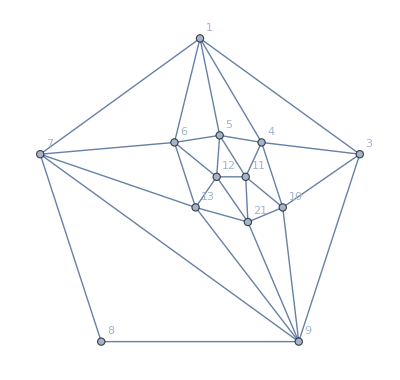
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
36 | 14 | 12 | 4 | 4 | 12 | 6 | 8 | 10 | 8 | 4 | 16 | 4 | 6 | 0 | 0 | 0 | 50
{-Graphics-, | 1 | 3 | 9 | 8 | 7
1 | 36
0 | 0
36 | 12
24 | 12
24 | 0
36
3 | 0
36 | 36
0 | 0
36 | 10
26 | 16
20
9 | 12
24 | 0
36 | 36
0 | 0
36 | 0
36
8 | 12
24 | 10
26 | 0
36 | 36
0 | 0
36
7 | 0
36 | 16
20 | 0
36 | 0
36 | 36
0}

```mathematica
AlfaBetaPentagon[g,2,{1,3,9,8,7}]
```

```mathematica
AlfaBetaPentagon[Graph[plantri[[100]]],2,{1,3,9,8,7}]
```

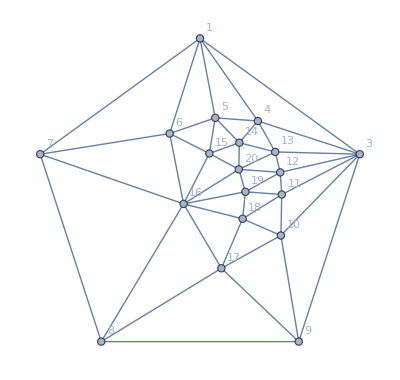
```mathematica
{{{{λ, Σ, α, α1, β, β1, γ, γ1, δ, δ1, ϵ, ϵ1, α+β+γ+δ+ϵ}, {192, 108, 77, 27, 45, 22, 64, 18, 74, 30, 40, 11, 300}}}, {{-Graphics-,{{, 1, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20}, {1, {{192}, {0}}, {{0}, {192}}, {{0}, {192}}, {{0}, {192}}, {{0}, {192}}, {{0}, {192}}, {{45}, {147}}, {{77}, {115}}, {{76}, {116}}, {{65}, {127}}, {{81}, {111}}, {{73}, {119}}, {{101}, {91}}, {{57}, {135}}, {{113}, {79}}, {{11}, {181}}, {{23}, {169}}, {{31}, {161}}, {{5}, {187}}}, {3, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{89}, {103}}, {{68}, {124}}, {{74}, {118}}, {{64}, {128}}, {{0}, {192}}, {{0}, {192}}, {{0}, {192}}, {{0}, {192}}, {{0}, {192}}, {{51}, {141}}, {{20}, {172}}, {{4}, {188}}, {{86}, {106}}, {{90}, {102}}, {{68}, {124}}, {{102}, {90}}}, {4, {{0}, {192}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{78}, {114}}, {{66}, {126}}, {{44}, {148}}, {{54}, {138}}, {{46}, {146}}, {{59}, {133}}, {{74}, {118}}, {{0}, {192}}, {{0}, {192}}, {{85}, {107}}, {{15}, {177}}, {{54}, {138}}, {{56}, {136}}, {{30}, {162}}, {{66}, {126}}}, {5, {{0}, {192}}, {{89}, {103}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{81}, {111}}, {{36}, {156}}, {{40}, {152}}, {{32}, {160}}, {{49}, {143}}, {{14}, {178}}, {{70}, {122}}, {{0}, {192}}, {{0}, {192}}, {{50}, {142}}, {{53}, {139}}, {{61}, {131}}, {{32}, {160}}, {{89}, {103}}}, {6, {{0}, {192}}, {{68}, {124}}, {{78}, {114}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{84}, {108}}, {{26}, {166}}, {{38}, {154}}, {{38}, {154}}, {{30}, {162}}, {{19}, {173}}, {{63}, {129}}, {{0}, {192}}, {{0}, {192}}, {{58}, {134}}, {{68}, {124}}, {{60}, {132}}, {{84}, {108}}}, {7, {{0}, {192}}, {{74}, {118}}, {{66}, {126}}, {{81}, {111}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{40}, {152}}, {{22}, {170}}, {{38}, {154}}, {{32}, {160}}, {{36}, {156}}, {{14}, {178}}, {{83}, {109}}, {{0}, {192}}, {{98}, {94}}, {{54}, {138}}, {{66}, {126}}, {{66}, {126}}}, {8, {{45}, {147}}, {{64}, {128}}, {{44}, {148}}, {{36}, {156}}, {{84}, {108}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{78}, {114}}, {{16}, {176}}, {{36}, {156}}, {{46}, {146}}, {{36}, {156}}, {{59}, {133}}, {{0}, {192}}, {{0}, {192}}, {{86}, {106}}, {{64}, {128}}, {{68}, {124}}}, {9, {{77}, {115}}, {{0}, {192}}, {{54}, {138}}, {{40}, {152}}, {{26}, {166}}, {{40}, {152}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{100}, {92}}, {{56}, {136}}, {{68}, {124}}, {{57}, {135}}, {{38}, {154}}, {{102}, {90}}, {{0}, {192}}, {{50}, {142}}, {{12}, {180}}, {{28}, {164}}}, {10, {{76}, {116}}, {{0}, {192}}, {{46}, {146}}, {{32}, {160}}, {{38}, {154}}, {{22}, {170}}, {{78}, {114}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{86}, {106}}, {{64}, {128}}, {{62}, {130}}, {{60}, {132}}, {{68}, {124}}, {{0}, {192}}, {{0}, {192}}, {{82}, {110}}, {{12}, {180}}}, {11, {{65}, {127}}, {{0}, {192}}, {{59}, {133}}, {{49}, {143}}, {{38}, {154}}, {{38}, {154}}, {{16}, {176}}, {{100}, {92}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{86}, {106}}, {{34}, {158}}, {{31}, {161}}, {{90}, {102}}, {{58}, {134}}, {{0}, {192}}, {{0}, {192}}, {{50}, {142}}}, {12, {{81}, {111}}, {{0}, {192}}, {{74}, {118}}, {{14}, {178}}, {{30}, {162}}, {{32}, {160}}, {{36}, {156}}, {{56}, {136}}, {{86}, {106}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{91}, {101}}, {{62}, {130}}, {{86}, {106}}, {{18}, {174}}, {{58}, {134}}, {{0}, {192}}, {{0}, {192}}}, {13, {{73}, {119}}, {{0}, {192}}, {{0}, {192}}, {{70}, {122}}, {{19}, {173}}, {{36}, {156}}, {{46}, {146}}, {{68}, {124}}, {{64}, {128}}, {{86}, {106}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{74}, {118}}, {{64}, {128}}, {{36}, {156}}, {{16}, {176}}, {{78}, {114}}, {{0}, {192}}}, {14, {{101}, {91}}, {{51}, {141}}, {{0}, {192}}, {{0}, {192}}, {{63}, {129}}, {{14}, {178}}, {{36}, {156}}, {{57}, {135}}, {{62}, {130}}, {{34}, {158}}, {{91}, {101}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{98}, {94}}, {{40}, {152}}, {{24}, {168}}, {{56}, {136}}, {{0}, {192}}}, {15, {{57}, {135}}, {{20}, {172}}, {{85}, {107}}, {{0}, {192}}, {{0}, {192}}, {{83}, {109}}, {{59}, {133}}, {{38}, {154}}, {{60}, {132}}, {{31}, {161}}, {{62}, {130}}, {{74}, {118}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{60}, {132}}, {{50}, {142}}, {{83}, {109}}, {{0}, {192}}}, {16, {{113}, {79}}, {{4}, {188}}, {{15}, {177}}, {{50}, {142}}, {{0}, {192}}, {{0}, {192}}, {{0}, {192}}, {{102}, {90}}, {{68}, {124}}, {{90}, {102}}, {{86}, {106}}, {{64}, {128}}, {{98}, {94}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{0}, {192}}, {{0}, {192}}, {{0}, {192}}}, {17, {{11}, {181}}, {{86}, {106}}, {{54}, {138}}, {{53}, {139}}, {{58}, {134}}, {{98}, {94}}, {{0}, {192}}, {{0}, {192}}, {{0}, {192}}, {{58}, {134}}, {{18}, {174}}, {{36}, {156}}, {{40}, {152}}, {{60}, {132}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{86}, {106}}, {{56}, {136}}}, {18, {{23}, {169}}, {{90}, {102}}, {{56}, {136}}, {{61}, {131}}, {{68}, {124}}, {{54}, {138}}, {{86}, {106}}, {{50}, {142}}, {{0}, {192}}, {{0}, {192}}, {{58}, {134}}, {{16}, {176}}, {{24}, {168}}, {{50}, {142}}, {{0}, {192}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}, {{100}, {92}}}, {19, {{31}, {161}}, {{68}, {124}}, {{30}, {162}}, {{32}, {160}}, {{60}, {132}}, {{66}, {126}}, {{64}, {128}}, {{12}, {180}}, {{82}, {110}}, {{0}, {192}}, {{0}, {192}}, {{78}, {114}}, {{56}, {136}}, {{83}, {109}}, {{0}, {192}}, {{86}, {106}}, {{0}, {192}}, {{192}, {0}}, {{0}, {192}}}, {20, {{5}, {187}}, {{102}, {90}}, {{66}, {126}}, {{89}, {103}}, {{84}, {108}}, {{66}, {126}}, {{68}, {124}}, {{28}, {164}}, {{12}, {180}}, {{50}, {142}}, {{0}, {192}}, {{0}, {192}}, {{0}, {192}}, {{0}, {192}}, {{0}, {192}}, {{56}, {136}}, {{100}, {92}}, {{0}, {192}}, {{192}, {0}}}},,274/809,0.33868974042027195}}, {{λ->192,α->77,α1->27,β->45,β1->22,γ->64,γ1->18,δ->74,δ1->30,ϵ->40,ϵ1->11}}}
```

```mathematica
AlfaBetaPentagon[Graph[plantri[[1000]]],17,{7,8,18,15,16}]
```

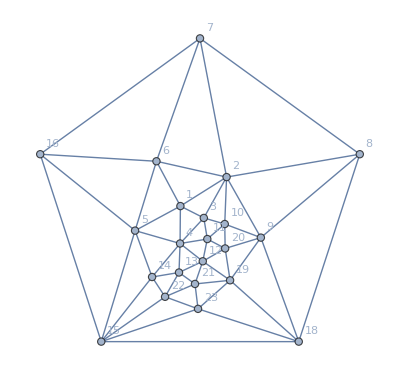
```mathematica
{{{{λ, Σ, α, α1, β, β1, γ, γ1, δ, δ1, ϵ, ϵ1, α+β+γ+δ+ϵ}, {416, 224, 91, 48, 92, 23, 191, 84, 78, 22, 188, 47, 640}}}, {{-Graphics-,{{, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 18, 19, 20, 21, 22, 23}, {1, {{416}, {0}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{155}, {261}}, {{116}, {300}}, {{137}, {279}}, {{159}, {257}}, {{192}, {224}}, {{116}, {300}}, {{152}, {264}}, {{196}, {220}}, {{144}, {272}}, {{141}, {275}}, {{65}, {351}}, {{104}, {312}}, {{28}, {388}}, {{100}, {316}}, {{34}, {382}}, {{132}, {284}}}, {2, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{203}, {213}}, {{108}, {308}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{125}, {291}}, {{23}, {393}}, {{83}, {333}}, {{60}, {356}}, {{42}, {374}}, {{214}, {202}}, {{233}, {183}}, {{83}, {333}}, {{249}, {167}}, {{158}, {258}}, {{140}, {276}}, {{49}, {367}}}, {3, {{0}, {416}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{219}, {197}}, {{128}, {288}}, {{184}, {232}}, {{74}, {342}}, {{218}, {198}}, {{0}, {416}}, {{0}, {416}}, {{231}, {185}}, {{96}, {320}}, {{117}, {299}}, {{53}, {363}}, {{38}, {378}}, {{71}, {345}}, {{40}, {376}}, {{95}, {321}}, {{52}, {364}}, {{114}, {302}}, {{183}, {233}}}, {4, {{0}, {416}}, {{203}, {213}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{174}, {242}}, {{16}, {400}}, {{143}, {273}}, {{16}, {400}}, {{153}, {263}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{134}, {282}}, {{167}, {249}}, {{146}, {270}}, {{128}, {288}}, {{228}, {188}}, {{167}, {249}}, {{169}, {247}}, {{24}, {392}}}, {5, {{0}, {416}}, {{108}, {308}}, {{219}, {197}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{214}, {202}}, {{35}, {381}}, {{150}, {266}}, {{45}, {371}}, {{108}, {308}}, {{172}, {244}}, {{120}, {296}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{124}, {292}}, {{64}, {352}}, {{78}, {338}}, {{48}, {368}}, {{186}, {230}}, {{116}, {300}}}, {6, {{0}, {416}}, {{0}, {416}}, {{128}, {288}}, {{174}, {242}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{242}, {174}}, {{85}, {331}}, {{183}, {233}}, {{55}, {361}}, {{76}, {340}}, {{102}, {314}}, {{115}, {301}}, {{214}, {202}}, {{0}, {416}}, {{29}, {387}}, {{176}, {240}}, {{65}, {351}}, {{102}, {314}}, {{61}, {355}}, {{96}, {320}}}, {7, {{155}, {261}}, {{0}, {416}}, {{184}, {232}}, {{16}, {400}}, {{214}, {202}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{212}, {204}}, {{78}, {338}}, {{118}, {298}}, {{167}, {249}}, {{111}, {305}}, {{72}, {344}}, {{92}, {324}}, {{0}, {416}}, {{91}, {325}}, {{52}, {364}}, {{53}, {363}}, {{84}, {332}}, {{127}, {289}}, {{113}, {303}}}, {8, {{116}, {300}}, {{0}, {416}}, {{74}, {342}}, {{143}, {273}}, {{35}, {381}}, {{242}, {174}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{242}, {174}}, {{67}, {349}}, {{73}, {343}}, {{137}, {279}}, {{94}, {322}}, {{191}, {225}}, {{78}, {338}}, {{0}, {416}}, {{221}, {195}}, {{63}, {353}}, {{66}, {350}}, {{79}, {337}}, {{101}, {315}}}, {9, {{137}, {279}}, {{0}, {416}}, {{218}, {198}}, {{16}, {400}}, {{150}, {266}}, {{85}, {331}}, {{212}, {204}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{145}, {271}}, {{205}, {211}}, {{70}, {346}}, {{150}, {266}}, {{84}, {332}}, {{60}, {356}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{97}, {319}}, {{80}, {336}}, {{200}, {216}}}, {10, {{159}, {257}}, {{0}, {416}}, {{0}, {416}}, {{153}, {263}}, {{45}, {371}}, {{183}, {233}}, {{78}, {338}}, {{242}, {174}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{125}, {291}}, {{85}, {331}}, {{115}, {301}}, {{147}, {269}}, {{86}, {330}}, {{68}, {348}}, {{203}, {213}}, {{0}, {416}}, {{53}, {363}}, {{118}, {298}}, {{88}, {328}}}, {11, {{192}, {224}}, {{125}, {291}}, {{0}, {416}}, {{0}, {416}}, {{108}, {308}}, {{55}, {361}}, {{118}, {298}}, {{67}, {349}}, {{145}, {271}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{198}, {218}}, {{113}, {303}}, {{143}, {273}}, {{82}, {334}}, {{65}, {351}}, {{154}, {262}}, {{0}, {416}}, {{127}, {289}}, {{55}, {361}}, {{72}, {344}}}, {12, {{116}, {300}}, {{23}, {393}}, {{231}, {185}}, {{0}, {416}}, {{172}, {244}}, {{76}, {340}}, {{167}, {249}}, {{73}, {343}}, {{205}, {211}}, {{125}, {291}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{204}, {212}}, {{10}, {406}}, {{91}, {325}}, {{81}, {335}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{140}, {276}}, {{244}, {172}}}, {13, {{152}, {264}}, {{83}, {333}}, {{96}, {320}}, {{0}, {416}}, {{120}, {296}}, {{102}, {314}}, {{111}, {305}}, {{137}, {279}}, {{70}, {346}}, {{85}, {331}}, {{198}, {218}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{223}, {193}}, {{38}, {378}}, {{42}, {374}}, {{221}, {195}}, {{84}, {332}}, {{0}, {416}}, {{0}, {416}}, {{100}, {316}}}, {14, {{196}, {220}}, {{60}, {356}}, {{117}, {299}}, {{0}, {416}}, {{0}, {416}}, {{115}, {301}}, {{72}, {344}}, {{94}, {322}}, {{150}, {266}}, {{115}, {301}}, {{113}, {303}}, {{204}, {212}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{177}, {239}}, {{111}, {305}}, {{12}, {404}}, {{57}, {359}}, {{152}, {264}}, {{0}, {416}}, {{230}, {186}}}, {15, {{144}, {272}}, {{42}, {374}}, {{53}, {363}}, {{134}, {282}}, {{0}, {416}}, {{214}, {202}}, {{92}, {324}}, {{191}, {225}}, {{84}, {332}}, {{147}, {269}}, {{143}, {273}}, {{10}, {406}}, {{223}, {193}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{0}, {416}}, {{226}, {190}}, {{65}, {351}}, {{127}, {289}}, {{0}, {416}}, {{0}, {416}}}, {16, {{141}, {275}}, {{214}, {202}}, {{38}, {378}}, {{167}, {249}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{78}, {338}}, {{60}, {356}}, {{86}, {330}}, {{82}, {334}}, {{91}, {325}}, {{38}, {378}}, {{177}, {239}}, {{0}, {416}}, {{416}, {0}}, {{188}, {228}}, {{65}, {351}}, {{184}, {232}}, {{141}, {275}}, {{126}, {290}}, {{116}, {300}}}, {18, {{65}, {351}}, {{233}, {183}}, {{71}, {345}}, {{146}, {270}}, {{124}, {292}}, {{29}, {387}}, {{91}, {325}}, {{0}, {416}}, {{0}, {416}}, {{68}, {348}}, {{65}, {351}}, {{81}, {335}}, {{42}, {374}}, {{111}, {305}}, {{0}, {416}}, {{188}, {228}}, {{416}, {0}}, {{0}, {416}}, {{244}, {172}}, {{189}, {227}}, {{163}, {253}}, {{0}, {416}}}, {19, {{104}, {312}}, {{83}, {333}}, {{40}, {376}}, {{128}, {288}}, {{64}, {352}}, {{176}, {240}}, {{52}, {364}}, {{221}, {195}}, {{0}, {416}}, {{203}, {213}}, {{154}, {262}}, {{0}, {416}}, {{221}, {195}}, {{12}, {404}}, {{226}, {190}}, {{65}, {351}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}, {{0}, {416}}, {{127}, {289}}, {{0}, {416}}}, {20, {{28}, {388}}, {{249}, {167}}, {{95}, {321}}, {{228}, {188}}, {{78}, {338}}, {{65}, {351}}, {{53}, {363}}, {{63}, {353}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{84}, {332}}, {{57}, {359}}, {{65}, {351}}, {{184}, {232}}, {{244}, {172}}, {{0}, {416}}, {{416}, {0}}, {{204}, {212}}, {{104}, {312}}, {{68}, {348}}}, {21, {{100}, {316}}, {{158}, {258}}, {{52}, {364}}, {{167}, {249}}, {{48}, {368}}, {{102}, {314}}, {{84}, {332}}, {{66}, {350}}, {{97}, {319}}, {{53}, {363}}, {{127}, {289}}, {{0}, {416}}, {{0}, {416}}, {{152}, {264}}, {{127}, {289}}, {{141}, {275}}, {{189}, {227}}, {{0}, {416}}, {{204}, {212}}, {{416}, {0}}, {{0}, {416}}, {{0}, {416}}}, {22, {{34}, {382}}, {{140}, {276}}, {{114}, {302}}, {{169}, {247}}, {{186}, {230}}, {{61}, {355}}, {{127}, {289}}, {{79}, {337}}, {{80}, {336}}, {{118}, {298}}, {{55}, {361}}, {{140}, {276}}, {{0}, {416}}, {{0}, {416}}, {{0}, {416}}, {{126}, {290}}, {{163}, {253}}, {{127}, {289}}, {{104}, {312}}, {{0}, {416}}, {{416}, {0}}, {{0}, {416}}}, {23, {{132}, {284}}, {{49}, {367}}, {{183}, {233}}, {{24}, {392}}, {{116}, {300}}, {{96}, {320}}, {{113}, {303}}, {{101}, {315}}, {{200}, {216}}, {{88}, {328}}, {{72}, {344}}, {{244}, {172}}, {{100}, {316}}, {{230}, {186}}, {{0}, {416}}, {{116}, {300}}, {{0}, {416}}, {{0}, {416}}, {{68}, {348}}, {{0}, {416}}, {{0}, {416}}, {{416}, {0}}}},,245/723,0.338865836791148}}, {{λ->416,α->91,α1->48,β->92,β1->23,γ->191,γ1->84,δ->78,δ1->22,ϵ->188,ϵ1->47}}}
```

```mathematica
AlfaBetaPentagon[Graph[plantri[[10000]]],1,{2,6,5,4,3}]
```

```mathematica
ChromaticPolynomial[Graph[plantri[[1000]]],4]
```

$Aborted

```mathematica
VertexCount[Graph[plantri[[100]]]]
```

20

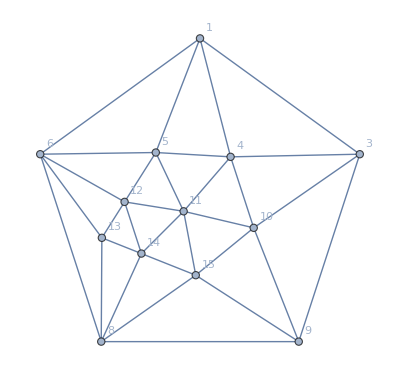

```mathematica
g=Graph[VertexDelete[Graph[{1<->2,1<->3,1<->4,1<->5,2<->8,2<->9,2<->3,3<->9,3<->10,3<->4,4<->10,4<->11,4<->5,5<->11,5<->12,8<->13,8<->14,8<->15,8<->9,9<->15,9<->10,10<->15,10<->11,11<->15,11<->14,11<->12,12<->14,12<->13,13<->14,14<->15,6<->1,6<->2,6<->5,6<->8,6<->12,6<->13}],{2}],GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

```mathematica
AlfaBetaPentagon33333[g_,center_,neighbours_]:=Block[
{ emptyg, sols, sols2,couplesols,f,
alfa,beta,gamma,delta,epsilon, 
alfa1,beta1,gamma1,delta1,epsilon1,
alfa2,beta2,gamma2,delta2,epsilon2,
lambda, full},

PrintTemporary["Solving g.." ];
emptyg=g;
sols=Solve[ToEquations[emptyg],SymbolRange[emptyg]];
full=ChromaticPolynomial[g,4];
PrintTemporary["Solved g" ];
lambda=Length[sols];
alfa=CalcEqual[sols,neighbours[[1]],neighbours[[3]]];
beta=CalcEqual[sols,neighbours[[1]],neighbours[[4]]];
gamma=CalcEqual[sols,neighbours[[2]],neighbours[[4]]];
delta=CalcEqual[sols,neighbours[[2]],neighbours[[5]]];
epsilon=CalcEqual[sols,neighbours[[3]],neighbours[[5]]];

PrintTemporary["Solving g 1/3.." ];
f=VertexContract[emptyg,{neighbours[[1]],neighbours[[3]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
gamma2=CalcEqual[sols2,neighbours[[2]],neighbours[[4]]];
delta1=CalcEqual[sols2,neighbours[[2]],neighbours[[5]]];


PrintTemporary["Solving g 1/4.." ];
f=VertexContract[emptyg,{neighbours[[1]],neighbours[[4]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
delta2=CalcEqual[sols2,neighbours[[2]],neighbours[[5]]];
epsilon1=CalcEqual[sols2,neighbours[[3]],neighbours[[5]]];

PrintTemporary["Solving g 2/4.." ];
f=VertexContract[emptyg,{neighbours[[2]],neighbours[[4]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
alfa1=CalcEqual[sols2,neighbours[[1]],neighbours[[3]]];
epsilon2=CalcEqual[sols2,neighbours[[3]],neighbours[[5]]];

PrintTemporary["Solving g 2/5.." ];
f=VertexContract[emptyg,{neighbours[[2]],neighbours[[5]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
alfa2=CalcEqual[sols2,neighbours[[1]],neighbours[[3]]];
beta1=CalcEqual[sols2,neighbours[[1]],neighbours[[4]]];

PrintTemporary["Solving g 3/5.." ];
f=VertexContract[emptyg,{neighbours[[3]],neighbours[[5]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
beta2=CalcEqual[sols2,neighbours[[1]],neighbours[[4]]];
gamma1=CalcEqual[sols2,neighbours[[2]],neighbours[[4]]];

Column[{
TableForm[
Map[{#}&,{lambda/24,full/24,Style[alfa/24,Red],alfa1/24,alfa2/24,Style[beta/24,Red],beta1/24,beta2/24,Style[gamma/24,Red],gamma1/24,gamma2/24,Style[delta/24,Red],delta1/24,delta2/24,Style[epsilon/24,Red],epsilon1/24,epsilon2/24,(alfa+beta+gamma+delta+epsilon)/24}],
TableHeadings->{{λ,Σ,α,α1,α2,β,β1,β2,γ,γ1,γ2,δ,δ1,δ2,ϵ,ϵ1,ϵ2,α+β+γ+δ+ϵ},None},
TableDirections->Row,
TableAlignments->Center,
TableSpacing->{1, 1}
],
ColorSSSMatrix[g,Graph[#,GraphLayout->"TutteEmbedding", VertexLabels->"Name"]&,neighbours,sols]
}
]
]
```

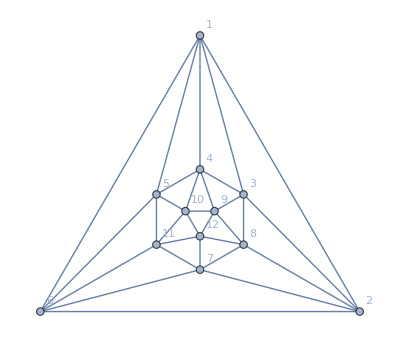
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
10 | 10 | 4 | 2 | 2 | 4 | 2 | 2 | 4 | 2 | 2 | 4 | 2 | 2 | 4 | 2 | 2 | 20
{-Graphics-, | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | 10
0 | 0
10 | 0
10 | 0
10 | 0
10 | 0
10 | 4
6 | 4
6 | 4
6 | 4
6 | 4
6 | 0
10
2 | 0
10 | 10
0 | 0
10 | 4
6 | 4
6 | 0
10 | 0
10 | 0
10 | 4
6 | 0
10 | 4
6 | 4
6
3 | 0
10 | 0
10 | 10
0 | 0
10 | 4
6 | 4
6 | 4
6 | 0
10 | 0
10 | 4
6 | 0
10 | 4
6
4 | 0
10 | 4
6 | 0
10 | 10
0 | 0
10 | 4
6 | 0
10 | 4
6 | 0
10 | 0
10 | 4
6 | 4
6
5 | 0
10 | 4
6 | 4
6 | 0
10 | 10
0 | 0
10 | 4
6 | 0
10 | 4
6 | 0
10 | 0
10 | 4
6
6 | 0
10 | 0
10 | 4
6 | 4
6 | 0
10 | 10
0 | 0
10 | 4
6 | 0
10 | 4
6 | 0
10 | 4
6
7 | 4
6 | 0
10 | 4
6 | 0
10 | 4
6 | 0
10 | 10
0 | 0
10 | 4
6 | 4
6 | 0
10 | 0
10
8 | 4
6 | 0
10 | 0
10 | 4
6 | 0
10 | 4
6 | 0
10 | 10
0 | 0
10 | 4
6 | 4
6 | 0
10
9 | 4
6 | 4
6 | 0
10 | 0
10 | 4
6 | 0
10 | 4
6 | 0
10 | 10
0 | 0
10 | 4
6 | 0
10
10 | 4
6 | 0
10 | 4
6 | 0
10 | 0
10 | 4
6 | 4
6 | 4
6 | 0
10 | 10
0 | 0
10 | 0
10
11 | 4
6 | 4
6 | 0
10 | 4
6 | 0
10 | 0
10 | 0
10 | 4
6 | 4
6 | 0
10 | 10
0 | 0
10
12 | 0
10 | 4
6 | 4
6 | 4
6 | 4
6 | 4
6 | 0
10 | 0
10 | 0
10 | 0
10 | 0
10 | 10
0,1 | {0.333333,1/3,60
180}
2 | {0.333333,1/3,60
180}
3 | {0.333333,1/3,60
180}
4 | {0.333333,1/3,60
180}
5 | {0.333333,1/3,60
180}
6 | {0.333333,1/3,60
180}
7 | {0.333333,1/3,60
180}
8 | {0.333333,1/3,60
180}
9 | {0.333333,1/3,60
180}
10 | {0.333333,1/3,60
180}
11 | {0.333333,1/3,60
180}
12 | {0.333333,1/3,60
180},1/3,0.333333}

```mathematica
AlfaBetaPentagon33333[Graph[plantri[[1]]],1,{2,3,4,5,6}]
```

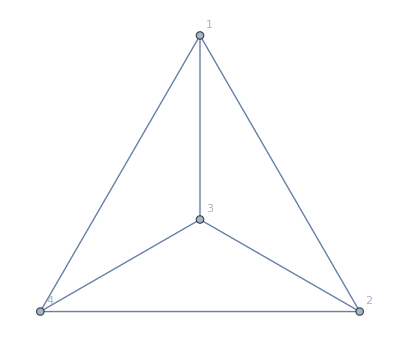
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
{-Graphics-, | 1 | 2 | 3 | 4
1 | 1
0 | 0
1 | 0
1 | 0
1
2 | 0
1 | 1
0 | 0
1 | 0
1
3 | 0
1 | 0
1 | 1
0 | 0
1
4 | 0
1 | 0
1 | 0
1 | 1
0,1 | {0.333333,1/3,2
6}
2 | {0.333333,1/3,2
6}
3 | {0.333333,1/3,2
6}
4 | {0.333333,1/3,2
6},1/3,0.333333}

```mathematica
AlfaBetaPentagon33333[CompleteGraph[4],1,{1,2,3,4,1}]
```

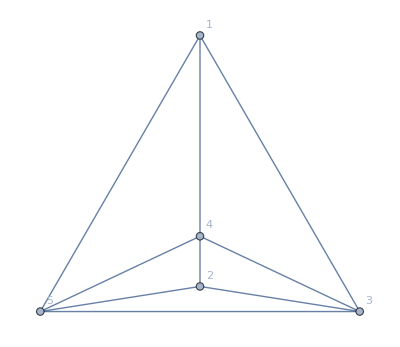
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 1
0 | 1
0 | 0
1 | 0
1 | 0
1
2 | 1
0 | 1
0 | 0
1 | 0
1 | 0
1
3 | 0
1 | 0
1 | 1
0 | 0
1 | 0
1
4 | 0
1 | 0
1 | 0
1 | 1
0 | 0
1
5 | 0
1 | 0
1 | 0
1 | 0
1 | 1
0,1 | {0.666667,2/3,4
6}
2 | {0.666667,2/3,4
6}
3 | {0.25,1/4,2
8}
4 | {0.25,1/4,2
8}
5 | {0.25,1/4,2
8},7/18,0.388889}

```mathematica
AlfaBetaPentagon33333[EdgeDelete[CompleteGraph[5],1<->2],1,{1,2,3,4,5}]
```